```mathematica
(* generates trial values of s, the cluster size *)
ClusterSizeWithALM[alpha_,length_,colors_]:=
With[{power=0,samples=10000},
JustVar["s",Clusters[alpha,length,colors,power,samples]]]
```

```mathematica
(* From a tally of s, returns a normalized distro func Subscript[w, s] *)
ClusterSizePDFWithTally[tally_]:=
Module[{f,v,w},
f = Function[{oldlist,nextitem}, (* unpacks tally *)
Module[{index=nextitem⟦1⟧,value=nextitem⟦2⟧,newlist=oldlist},
newlist⟦index⟧=value;newlist]];
v=Fold[f,ConstantArray[0,Max[tally⟦All,1⟧]],tally];
v = v / Total[v]; (* normalizes *)
w[pos_]:=If[pos>Length[v],0,v⟦pos⟧]; (* converts to func *)
w]
```

```mathematica
(* returns Subscript[w, s], based on simulation *)
ClusterSizePDFWithALM[a_,l_,m_]:=
ClusterSizePDFWithTally @ Tally @ ClusterSizeWithALM[a,l,m]
```

```mathematica
(* returns Subscript[w, s], based on candidate analytic expression *)
FinkClusterSizePDFWithALM[a_,l_,m_]:=Function[s,m 1/(s!)1/m^s((m-1)/m)^(l (a-1) s)s^(s-1)(l (a-1))^(s-1)]
```

```mathematica
(* Visually compares simulated and analytical distro *)
CompareDistros[a_,l_,m_]:=
With[
{maxS=6,
vf=FinkClusterSizePDFWithALM[a,l,m],
vd=ClusterSizePDFWithALM[a,l,m]},
Show[
DiscretePlot[vd[s],{s,maxS},ExtentSize->Full,PlotMarkers->{"Point",Large}],
Plot[vf[s],{s,0,maxS}],
PlotRange->{{0,maxS},{0,1}}]]
```

```mathematica
NumberCompareDistros[a_,l_,m_]:=
With[
{maxS=6,
vf=FinkClusterSizePDFWithALM[a,l,m],
vd=ClusterSizePDFWithALM[a,l,m]},
Table[{s,vd[s],vf[s]},
{s,1,maxS,1}]]
```

```mathematica
NumberCompareDistros[2,10,12] // N // TableForm
```

1. | 0.4285 | 0.418904
2. | 0.1713 | 0.146234
3. | 0.1073 | 0.0765723
4. | 0.0745 | 0.0475207
5. | 0.0489 | 0.0324001
6. | 0.0341 | 0.0234533

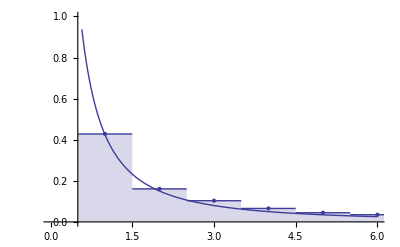

```mathematica
CompareDistros[2,15,18]
```

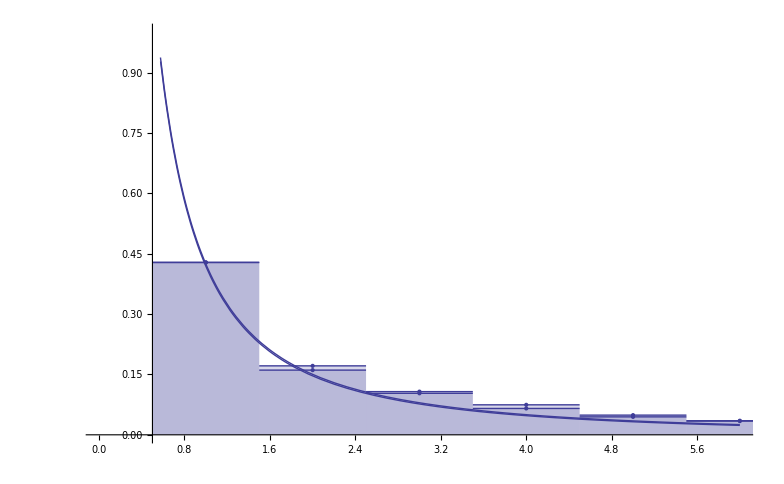

```mathematica
Show[%127,%128]
```

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

```mathematica
?Plot3D
```

Plot3D[f,{x,x_min,x_max},{y,y_min,y_max}] generates a three-dimensional plot of f as a function of x and y. 
Plot3D[{f_1,f_2,…},{x,x_min,x_max},{y,y_min,y_max}] plots several functions.

```mathematica
?L
```

Information::notfound: Symbol "L" not found.

```mathematica
FinkClusterSizePDFWithALM[2,L,2] [[2]] /. {s$ ->s} // Simplify
```

```mathematica
(2^(1-(1+L) s) L^(-1+s) s^(-1+s))/(s!)
```

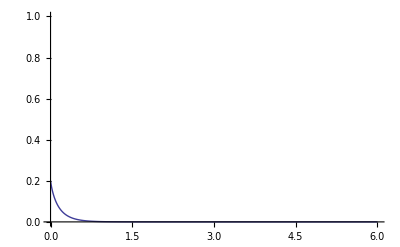

```mathematica
With[{m=2},
Plot[s*(FinkClusterSizePDFWithALM[2,10,m][s]),{s,0,6},PlotRange->{{0,6},{0,1}}]]
```

```mathematica
Plot3D[s*(FinkClusterSizePDFWithALM[2,10,m][s]),{s,0,6},{m,2,15},PlotRange->{{0,6},{2,15},{0,1}}]
```

-Graphics3D-

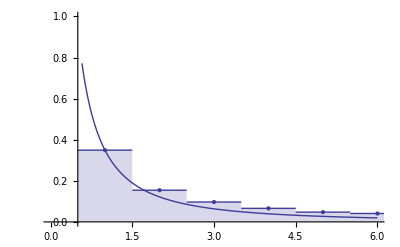
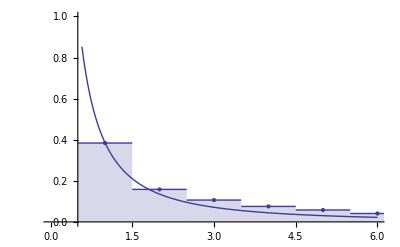
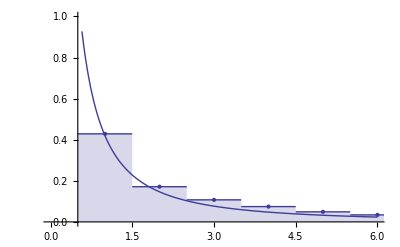
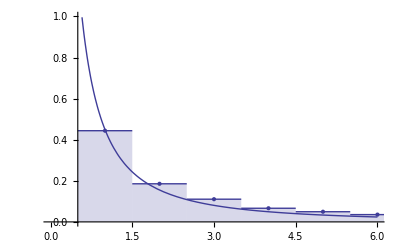
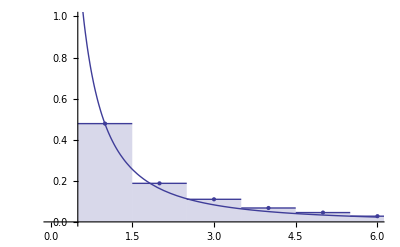
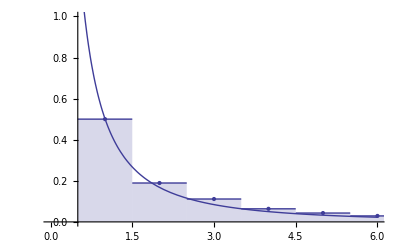
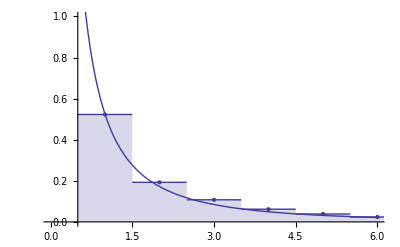
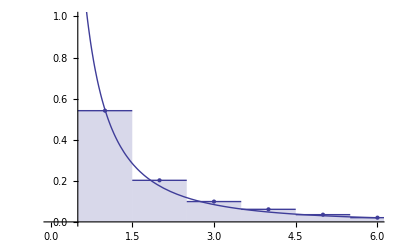

```mathematica
Table[CompareDistros[2,10,m],{m,10,20,1}]
```

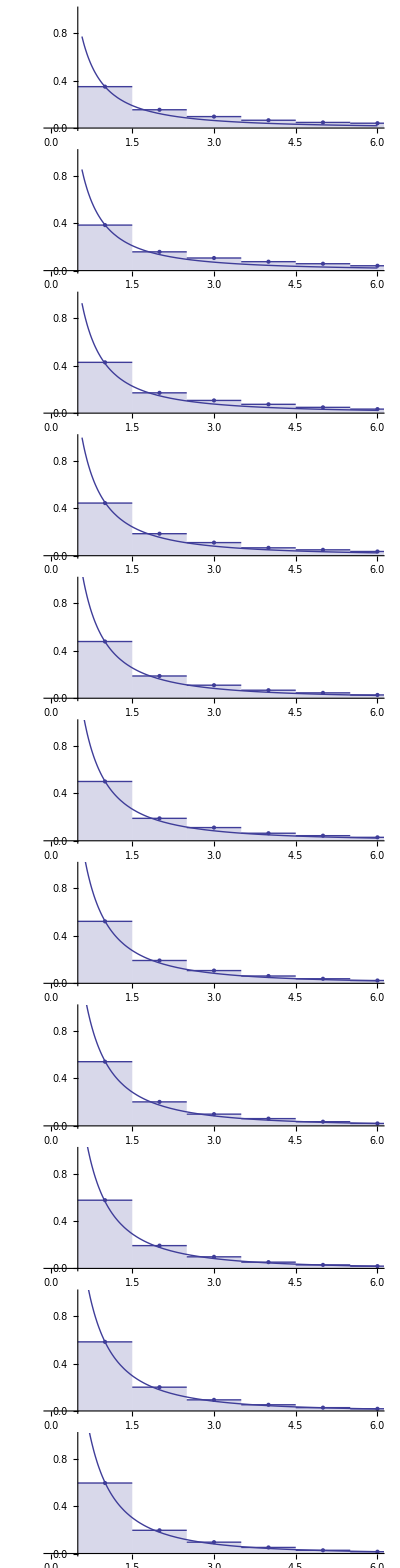

```mathematica
% // ColumnForm
```

```mathematica
?DiscretePlot3D
```

DiscretePlot3D[expr,{i,i_min,i_max},{j,j_min,j_max}] generates a plot of the values of expr when i runs from i_min to i_max and j runs from j_min to j_max.
DiscretePlot3D[expr,{i,i_min,i_max,di},{j,j_min,j_max,dj}] uses steps di and dj.
DiscretePlot3D[expr,{i,{i_1,i_2,…}},{j,{j_1,j_2,…}}] uses successive i values i_1, i_2, … and j values j_1,  j_2, …. 
DiscretePlot3D[{expr_1,expr_2,…},…,…] plots the values of all the expr_i.

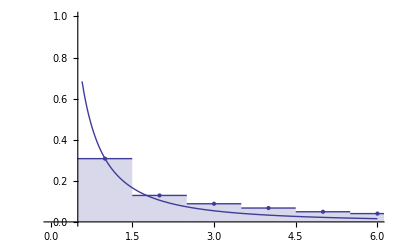

```mathematica
CompareDistros[2,10,9]
```

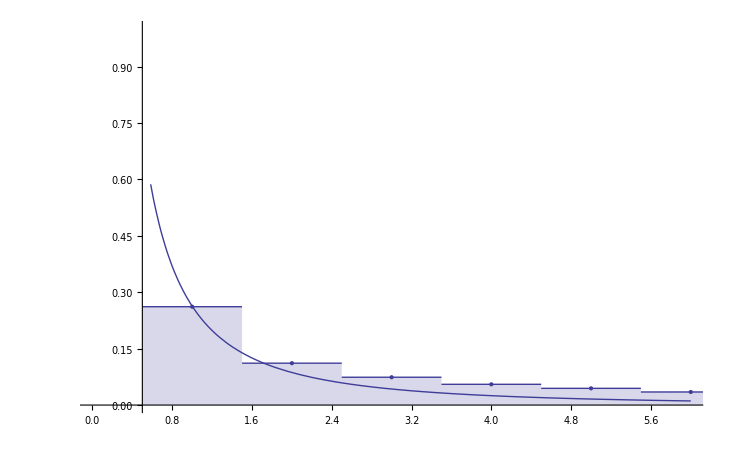

```mathematica
CompareDistros[2,10,8]
```

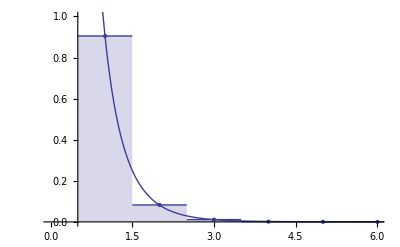

```mathematica
CompareDistros[2,10,100]
```

```mathematica
CompareDistros[2,10,10]
```

-Graphics-

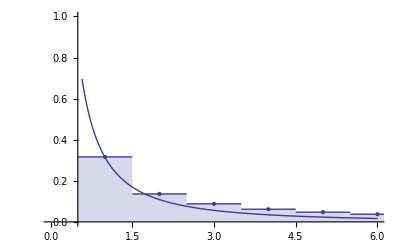

```mathematica
CompareDistros[2,11,10]
```

```mathematica
CompareDistros[2,10,100]
```

-Graphics-

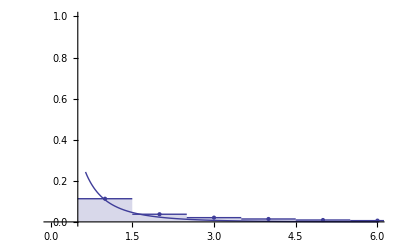

```mathematica
CompareDistros[2,10,5]
```

## Examining analytical sum for Σ s w_s

```mathematica
With[{a=2,l=5,m=20},
With[{r=l/m((m-1)/m)^(l (a-1))},
{r,
m/l Sum[s^s/(s!)r^s,{s,1,2000}],
m/(m-l (a-1))}]]  // N
```

{0.193445,1.31814,1.33333}

```mathematica
Hold[l/m((m-1)/m)^(l (a-1))] /. {a->2,l->5,m->20}
```

Hold[5/20 ((20-1)/20)^(5 (2-1))]

```mathematica
Plus[{1,2,3}]
```

{1,2,3}

```mathematica
With[{x=5},
Sum[FinkClusterSizePDFWithALM[a,l,m][s],{s,1,Infinity}]] // FullSimplify
```

∑_(s=1)^∞ (((-1+a) l)^(-1+s) ((-1+m)/m)^((-1+a) l s) m^(1-s) s^(-1+s))/(s!)